```mathematica
SetDirectory[NotebookDirectory[]];
```

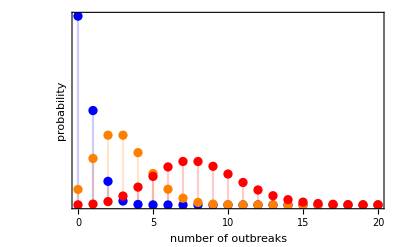

```mathematica
λ1 = 0.5;
λ2 = 3;
λ3 = 8;
g1=DiscretePlot[{PDF[PoissonDistribution[λ1],x],PDF[PoissonDistribution[λ2],x],PDF[PoissonDistribution[λ3],x]},{x,0,20},PlotStyle->{Blue,Orange,Red},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"number of outbreaks","probability"},BaseStyle->Medium]
```

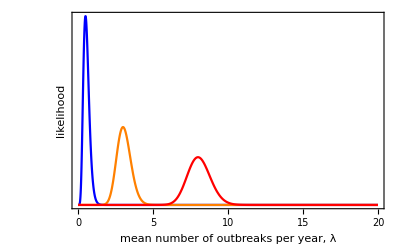

```mathematica
data1 = {1,2,0,0,2,1,0,0,1,0,0,0,0,0};
data2 = {3,2,1,4,2,1,6,3,1,3,5,1,6,4};
data3 = {6,10,6,7,6,12,8,12,11,12,6,6,6,4};
int1 = NIntegrate[Likelihood[PoissonDistribution[λ],data1],{λ,0,∞}];
int2 = NIntegrate[Likelihood[PoissonDistribution[λ],data2],{λ,0,∞}];
int3 = NIntegrate[Likelihood[PoissonDistribution[λ],data3],{λ,0,∞}];
g2=Plot[{Likelihood[PoissonDistribution[λ],data1]/int1,Likelihood[PoissonDistribution[λ],data2]/int2,Likelihood[PoissonDistribution[λ],data3]/int3},{λ,0,20},PlotRange->{{0,20},Full},PlotStyle->{Blue,Orange,Red},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"mean number of outbreaks per year, λ","likelihood"},BaseStyle->Medium]
```

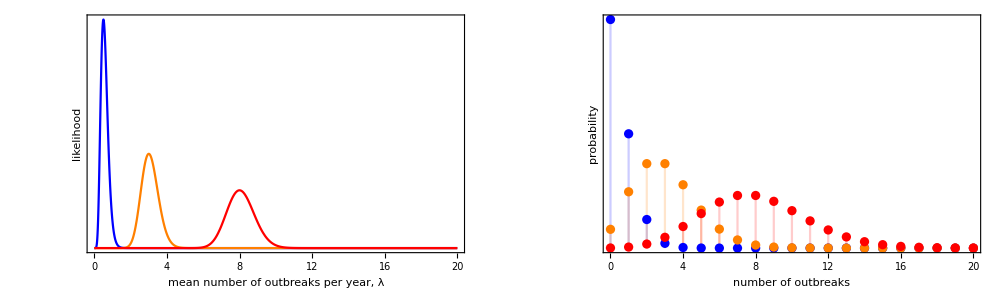

```mathematica
Show[GraphicsRow[{g2,g1}],ImageSize->1000]
```

```mathematica
Export["Distributions_poissonLegionella.pdf",gFinal]
```

Distributions_poissonLegionella.pdf